max n Vs r/L plot code. 
k = r/L, to get maximum n I set a and s to zero

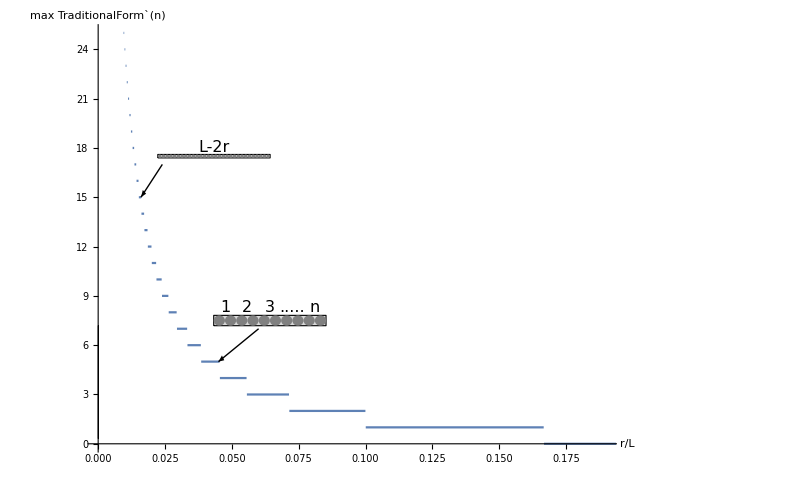

```mathematica
nm[k_]:={1/(4 k)-1/2};
a1=0;a2=0;a3=0;
nmax=Plot[Floor[nm[k]],{k,0,0.2},ImageSize->800,PlotRange->{{0,0.19},{0,25}},AxesLabel ->{"r/L","max TraditionalForm`(n) "},LabelStyle->{FontSize->16,Bold,Black},AxesStyle->Thick,Epilog->{Arrowheads[Medium],Arrow[{{0.23,3},{0.20,1}}],Arrow[{{0.06,7},{0.045,5}}],Arrow[{{0.024,17},{0.016,15}}],Text[Style["r",Black,16,Italic],{0.2195+0.0105*2.5,5}],Text[Style["L-2r",Black,16,Italic],{0.04329999999999999,18}],Text[Style["1",Black,16,Italic],{0.04531+0.0105*3-0.0105*4+a1*0.005+0.0105/5*6,8+1.575/5}],
Text[Style["2",Black,16,Italic],{0.04531+0.0105*3-0.0105*4+a1*0.005+0.0105/5*10,8+1.575/5}],
Text[Style["3",Black,16,Italic],{0.04531+0.0105*3-0.0105*4+a1*0.005+0.0105/5*14,8+1.575/5}],
Text[Style[".....",Black,16,Italic],{0.04531+0.0105*3-0.0105*4+a1*0.005+0.0105/5*18,8+1.575/5}],
Text[Style["n",Black,16,Italic],{0.04531+0.0105*3-0.0105*4+a1*0.005+0.0105/5*22,8+1.575/5}],
Text[Style["1",Black,16,Italic],{0.2195+0.0105*3-0.0105*2+a1*0.005,5.25+1.575}]}];
Cir1=Graphics[{Gray,Disk[{.2195,4.75},{0.0105,1.575}],Disk[{0.2195+0.0105*2+a1*0.005,4.75},{0.0105,1.575}]}];


cir2=Graphics[{Gray,Disk[{0.04531,7.5},{0.0105/5,1.575/5}],Disk[{0.04531+0.0105/5*2+a2*0.005,7.5},{0.0105/5,1.575/5} ],Disk[{0.04531+0.0105/5*4+a2*0.005*1.5,7.50},{0.0105/5,1.575/5}],Disk[{0.04531+0.0105/5*6+a2*0.005*1.5,7.5},{0.0105/5,1.575/5}],Disk[{0.04531+0.0105/5*8+a2*0.005*3.5,7.5},{0.0105/5,1.575/5}],Disk[{0.04531+0.0105/5*10+a2*0.005*3.5,7.5},{0.0105/5,1.575/5}],Disk[{0.04531+0.0105/5*12+a2*0.005*1.5,7.5},{0.0105/5,1.575/5}],Disk[{0.04531+0.0105/5*14+a2*0.005*1.5,7.5},{0.0105/5,1.575/5}],Disk[{0.04531+0.0105/5*16+a2*0.005*3.5,7.5},{0.0105/5,1.575/5}],Disk[{0.04531+0.0105/5*18+a2*0.005*3.5,7.5},{0.0105/5,1.575/5}]}];


line=Graphics[Line[{{0.2195+0.0105*2+a1*0.005,4.75},{0.2195+0.0105*3+a1*0.005,4.75}}]];

cir3 = Graphics[{Gray,Disk[{0.023,17.5},{0.0105/15,1.575/15}],Disk[{0.023+0.0105/15*2+a3*0.005,17.5},{0.0105/15,1.575/15} ],Disk[{0.023+0.0105/15*4+a3*0.005*1.5,17.5},{0.0105/15,1.575/15}],Disk[{0.023+0.0105/15*6+a3*0.005*1.5,17.5},{0.0105/15,1.575/15}],Disk[{0.023+0.0105/15*8+a3*0.005*2.5,17.5},{0.0105/15,1.575/15}],Disk[{0.023+0.0105/15*10+a3*0.005*2.5,17.5},{0.0105/15,1.575/15}],Disk[{0.023+0.0105/15*12+a3*0.005*3.5,17.5},{0.0105/15,1.575/15}],Disk[{0.023+0.0105/15*14+a3*0.005*3.5,17.5},{0.0105/15,1.575/15}],Disk[{0.023+0.0105/15*16+a3*0.005*2,17.5},{0.0105/15,1.575/15}],Disk[{0.023+0.0105/15*18+a3*0.005*2,17.5},{0.0105/15,1.575/15}],Disk[{0.023+0.0105/15*20,17.5},{0.0105/15,1.575/15}],Disk[{0.023+0.0105/15*22+a3*0.005,17.5},{0.0105/15,1.575/15} ],Disk[{0.023+0.0105/15*24+a3*0.005*1.5,17.5},{0.0105/15,1.575/15}],Disk[{0.023+0.0105/15*26+a3*0.005*1.5,17.5},{0.0105/15,1.575/15}],Disk[{0.023+0.0105/15*28+a3*0.005*2.5,17.5},{0.0105/15,1.575/15}],Disk[{0.023+0.0105/15*30+a3*0.005*2.5,17.5},{0.0105/15,1.575/15}],Disk[{0.023+0.0105/15*32+a3*0.005*3.5,17.5},{0.0105/15,1.575/15}],Disk[{0.023+0.0105/15*34+a3*0.005*3.5,17.5},{0.0105/15,1.575/15}],Disk[{0.023+0.0105/15*36+a3*0.005*2,17.5},{0.0105/15,1.575/15}],Disk[{0.023+0.0105/15*38+a3*0.005*2,17.5},{0.0105/15,1.575/15}],
Disk[{0.023+0.0105/15*40+a3*0.005*1.5,17.5},{0.0105/15,1.575/15}],Disk[{0.023+0.0105/15*42+a3*0.005*1.5,17.5},{0.0105/15,1.575/15}],Disk[{0.023+0.0105/15*44+a3*0.005*2.5,17.5},{0.0105/15,1.575/15}],Disk[{0.023+0.0105/15*46+a3*0.005*2.5,17.5},{0.0105/15,1.575/15}],Disk[{0.023+0.0105/15*48+a3*0.005*3.5,17.5},{0.0105/15,1.575/15}],Disk[{0.023+0.0105/15*50+a3*0.005*3.5,17.5},{0.0105/15,1.575/15}],Disk[{0.023+0.0105/15*52+a3*0.005*2,17.5},{0.0105/15,1.575/15}],Disk[{0.023+0.0105/15*54+a3*0.005*2,17.5},{0.0105/15,1.575/15}],
Disk[{0.023+0.0105/15*56+a3*0.005*2,17.5},{0.0105/15,1.575/15}],Disk[{0.023+0.0105/15*58+a3*0.005,17.5},{0.0105/15,1.575/15} ]}];

rect1=Graphics[{FaceForm[],EdgeForm[{Thick,Black}],Rectangle[{0.2195+0.0105*3-0.0105*4+a1*0.005,4.75-1.575
},{0.2195+0.0105*3+a1*0.005,4.75+1.575
}]}];

rect2=Graphics[{FaceForm[LightGray],EdgeForm[{Thick,Black}],Rectangle[{0.04531+0.0105*3-0.0105*4+a1*0.005+0.0105/5*4,7.5-1.575/5
},{0.04531+0.0105*3+a1*0.005+0.0105/5*4,7.5+1.575/5
}]}];

rect2a=Graphics[{FaceForm[White],EdgeForm[{Thick,Black}],Rectangle[{0.04321`+3*0.0105/5,7.5-1.575/5
},{0.04321`+5*0.0105/5,1.575/5}]}];

rect3=Graphics[{FaceForm[],EdgeForm[{Thick,Black}],Rectangle[{0.023+0.0105*3-0.0105*4+a1*0.005+14*0.0105/15,17.5-1.575/15
},{0.023+0.0105*3+a1*0.005+14*0.0105/15,17.5+1.575/15}]}];

Show[nmax,Cir1,line,rect1,rect2,rect2a,cir2,rect3,cir3]
```

```mathematica
0.04531+0.0105*3-0.0105*4+0.0105/5*4
```

0.04321